# 2D First-Passage time

## Drift towards the equilibrium at (x, xh) = (0, 0) with an absorbing boundary at xh=1. Initial condition is a wide distribution which narrows on approach to the fixed point.

## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP=-D[p[t, x, xh], t]+λ*D[xh*p[t, x, xh], x]+D[xh*p[t, x, xh], xh]-κ*D[x*p[t, x, xh],xh]+λ*D[p[t, x, xh],{x,2}]+D[p[t, x, xh],{xh,2}]
```

p[t,x,xh]+xh p^(0,0,1)[t,x,xh]-x κ p^(0,0,1)[t,x,xh]+p^(0,0,2)[t,x,xh]+xh λ p^(0,1,0)[t,x,xh]+λ p^(0,2,0)[t,x,xh]-p^(1,0,0)[t,x,xh]

## Choose the parameter values

```mathematica
λs = {0.2, 0.5, 1};
κs = {0.2,0.5, 1};
params = Flatten[Table[{λ->l, κ->k}, {l, λs}, {k, κs}], 1]
legend =  Flatten[Table["λ="<>ToString[l]<>"; "<> "κ="<>ToString[k], {l, λs},{k, κs}], 1];
eigenvectors = Table[{{(1+√(1-4 κ λ))/(2 κ),1},{-(-1+√(1-4 κ λ))/(2 κ),1}}/.p, {p, params}]
eigenvalues = Table[{1/2 (1-√(1-4 κ λ)),1/2 (1+√(1-4 κ λ))}/.p ,{p,params}]
```

{{λ→0.2,κ→0.2},{λ→0.2,κ→0.5},{λ→0.2,κ→1},{λ→0.5,κ→0.2},{λ→0.5,κ→0.5},{λ→0.5,κ→1},{λ→1,κ→0.2},{λ→1,κ→0.5},{λ→1,κ→1}}

{{{4.79129,1},{0.208712,1}},{{1.7746,1},{0.225403,1}},{{0.723607,1},{0.276393,1}},{{4.43649,1},{0.563508,1}},{{1.,1},{1.,1}},{{0.5+0.5 ⅈ,1},{0.5-0.5 ⅈ,1}},{{3.61803,1},{1.38197,1}},{{1.+1. ⅈ,1},{1.-1. ⅈ,1}},{{1/2 (1+ⅈ √3),1},{1/2 (1-ⅈ √3),1}}}

{{0.0417424,0.958258},{0.112702,0.887298},{0.276393,0.723607},{0.112702,0.887298},{0.5,0.5},{0.5-0.5 ⅈ,0.5+0.5 ⅈ},{0.276393,0.723607},{0.5-0.5 ⅈ,0.5+0.5 ⅈ},{1/2 (1-ⅈ √3),1/2 (1+ⅈ √3)}}

## Set up the mesh, boundary conditions, and initial condition

{{3/2,1/2},{1/2,1}}

{p[t,-15,xh]==0,p[t,15,xh]==0,p[t,x,15]==0,p[t,x,1]==0}

ElementMesh[{{-15.,15.},{1.,15.}},{QuadElement[<4275>]}]

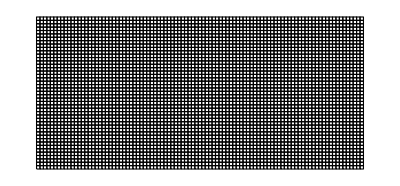

```mathematica
xf=15;
tf=12;
icPos = {5, 5};
icVar = {{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[9]] (*Choose widest s.s. distribution of the parameter values*)
ic0 = N[Table[PDF[MultinormalDistribution[icPos,icVar], {x, xh}], {i, params}]];
icSS = N[Table[PDF[MultinormalDistribution[icPos,{{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.p], {x, xh}], {p, params}]];
bcs = {p[t,-xf, xh]==0,
           p[t, xf, xh]==0,
           p[t, x, xf]==0,
(*(D[p[t,x,xh], xh])/.xh->0 ==0,*)
(*FP==NeumannValue[0, xh==xf],*)
           p[t, x, 1]==0
}

Needs["NDSolve`FEM`"]
mesh=ToElementMesh[Rectangle[{-xf, 1}, {xf, xf}],MaxCellMeasure->0.1 ]
mesh["Wireframe"]
```

## Calculate the probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==0,p[0, x,xh]== ic}, bcs],
                                   p,{t,0,tf},Element[{x, xh}, mesh], 
Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}}];
Return[p/.N[[1]]];
]
```

```mathematica
sols=MapThread[NDSolverParams, {params, icSS}];
flux = Table[Derivative[0,0,1][sol], {sol, sols}];
```

```mathematica
Clear[c]
```

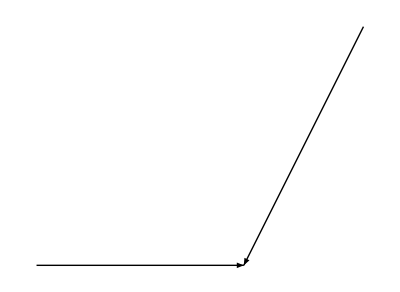

```mathematica
c[t_]:= ContourPlot[sols[[9]][t, x, xh], {x, -xf,xf}, {xh, 1, xf}, AxesLabel->{x, xh}, PlotRange->{-0.01, 0.1}, PlotLegends->Automatic, ColorFunction->ColorData[{"CherryTones",{-0.01,0.2}}],ColorFunctionScaling->False, FrameLabel->{"x","xh"}];
eigens =eigenvectors[[9]];
If [eigens∈Reals,
arrows= Graphics[Arrow/@{{{eigens[[1,1]],eigens[[1,2]]}, {0,0}},{{eigens[[2,1]],eigens[[1,2]]}, {0,0}}}],
arrows= Graphics[Arrow/@{{{Re[eigens[[1,1]]],Re[eigens[[1,2]]]}, {0,0}},{{Im[eigens[[2,1]]],Im[eigens[[1,2]]]}, {0,0}}}]]
```

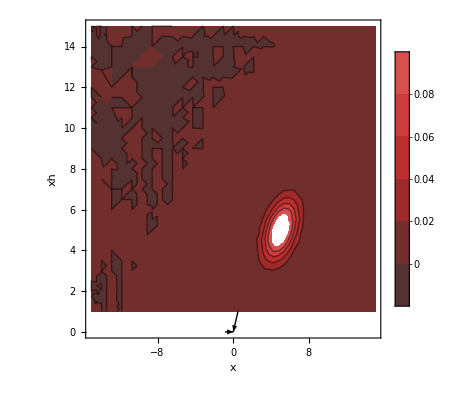

```mathematica
Show[c[0], arrows]
```

```mathematica
Manipulate[Show[c[t], arrows], {t, 0, tf}]
```

## Integrate the flux in t to get q(x)

At a given value of x, integrate in time

```mathematica
xrange = N[Range[-xf, xf, 2*xf/50]]
```

{-15.,-14.4,-13.8,-13.2,-12.6,-12.,-11.4,-10.8,-10.2,-9.6,-9.,-8.4,-7.8,-7.2,-6.6,-6.,-5.4,-4.8,-4.2,-3.6,-3.,-2.4,-1.8,-1.2,-0.6,0.,0.6,1.2,1.8,2.4,3.,3.6,4.2,4.8,5.4,6.,6.6,7.2,7.8,8.4,9.,9.6,10.2,10.8,11.4,12.,12.6,13.2,13.8,14.4,15.}

```mathematica
nintxsolve[xr_, s_]:=Module[{t, x},
n =Table[NDSolveValue[{g'[t]==s[t, x, 1],g[0]==0},g,{t,0,tf}, Method->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}][tf], {x, xr}];
Return[n];
];
```

```mathematica
xvals = Table[nintxsolve[xrange,flu], {flu, flux}];
```

Interpolate to get the distribution in x

```mathematica
X=Table[Interpolation[Transpose@{xrange, xval}][x], {xval, xvals}];
```

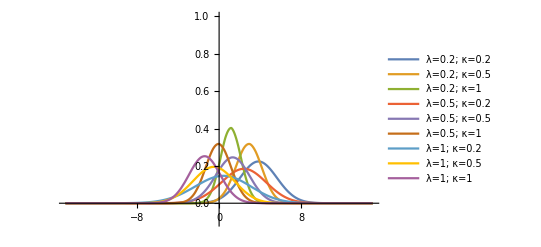

```mathematica
Plot[X, {x, -xf, xf}, PlotLegends->legend, PlotRange->{-0.1, 1}]
```

```mathematica
norms = Table[NIntegrate[xp, {x, -xf, xf}, WorkingPrecision->16], {xp, X}]
means = Table[NIntegrate[xp*x, {x, -xf, xf}, WorkingPrecision->16], {xp, X}]
second = Table[NIntegrate[xp*x*x, {x, -xf, xf}, WorkingPrecision->16], {xp, X}];
vars = second-means^2
diff = vars/means;
```

{1.01588,1.01457,0.984733,0.854199,0.914248,1.0154,1.0133,1.01144,1.00005,1.00005,1.01143,1.01102,1.00769,0.987915,0.954891,1.01675,1.00999,0.989839,0.965463,0.896131,1.02311,0.992543,0.956731,0.912909,0.819516}

{4.596398506191455,4.470245227815382,3.590885848949273,1.575715512394574,0.4131862018942841,4.120229106186104,3.907122871784619,2.902341071710239,1.151329548676207,-0.05829464972699604,2.756168622867118,2.415630288284544,1.287098985259311,-0.05251267493392046,-0.9925274400733476,0.7038148480995659,0.3197513780257882,-0.5477310185893746,-1.359096352517307,-1.854793763714789,-2.736180276295674,-3.00763642752861,-3.060306225817841,-3.056354492399459,-2.827705639501402}

{5.354300848556,2.5917136083784,1.3710620292759,1.04477816925716,0.311802004095051,6.09387322482567,3.1176994610706,1.5442983056328,0.983135296435351,0.463169199613746,8.50450506880593,4.80904403859456,2.67689563741742,1.52789714157959,0.853283409386468,13.0658356358816,7.66370307655453,4.04625337098854,2.3356335435273,1.67287096652872,22.1259930072504,12.8839231964194,6.67153806502043,4.3828934767096,3.78645176973895}

```mathematica
λs = { 0.1, 0.2, 0.5, 1, 2};
σs = {0.1, 0.2, 0.5, 1, 2};
grid = Flatten[Table[{l, s}, {l, λs}, {s, σs}], 1];
v = Table[{va}, {va, vars}];
```

```mathematica
varArray = ArrayReshape[vars, {5, 5}];
meanArray = ArrayReshape[means, {5, 5}];
diffArray = ArrayReshape[diff, {5, 5}];
```

```mathematica
xticks = Transpose[{{1, 2, 3, 4, 5}, λs}];
yticks = Transpose[{{1, 2, 3, 4, 5}, σs}];
```

```mathematica
ArrayPlot[varArray, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"var(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[meanArray, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[diffArray, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"var(x)/mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]
```

-Graphics-

-Graphics-

-Graphics-

## Integrate to get the survival probability and first-passage times

```mathematica
nintrange[tr_, s_]:=Module[{x, xh},
n = Table[NIntegrate[s[x,xh,t], {x,xh}∈s["ElementMesh"],  Method->"InterpolationPointsSubdivision"],{t, tr}];
Return[n];
];trange = N[Range[0, tf, tf/50]];
```

```mathematica
S= Table[nintrange[trange,sol], {sol, sols}];
```

NIntegrate::femonly: Method InterpolationPointsSubdivision is not applicable for this region domain. Continuing with the "FiniteElement" method.

General::stop: Further output of NIntegrate::femonly will be suppressed during this calculation.

```mathematica
s=Table[Interpolation[Transpose@{trange, Sp}][t], {Sp, S}];
f = Table[-D[sp, t], {sp, s}];
```

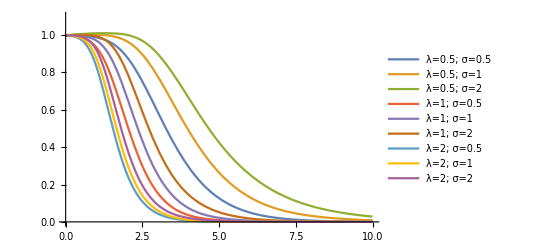

```mathematica
Plot[s,{t, 0, tf}, PlotRange->{0,1.1}, PlotLegends->legend]
```

## Calculate first-passage time probability

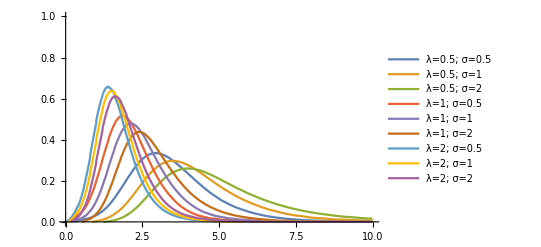

```mathematica
Plot[f,{t, 0, tf}, PlotRange->{0, 1} , PlotLegends->legend]
```

```mathematica
norms = Table[NIntegrate[fp, {t, 0, tf}], {fp, f}]
means = Table[NIntegrate[fp*t, {t, 0, tf}], {fp, f}]
second = Table[NIntegrate[fp*t*t, {t, 0, tf}], {fp, f}]
vars = second-means^2
```

{0.996601,0.988501,0.968595,0.997091,0.997098,0.996506,0.99702,0.997011,0.997015}

{3.45462,4.16734,4.76701,2.15921,2.49471,2.90643,1.63569,1.75965,1.93072}

{13.817,19.8175,25.9578,5.47297,7.21248,9.71744,3.18336,3.64939,4.37198}

{1.88255,2.45074,3.23341,0.810779,0.988891,1.27009,0.507871,0.553031,0.644305}

WolframAlphaQueryResults